```mathematica
SetDirectory[NotebookDirectory[]];
```

Note plots produced here may differ slightly from those in paper . This is because original notebook for plots used "PolygonPlotMarkers" package . In order to avoid having to include this package with the notebook I opted here to just use basic Mathematica natively supported polygons .

## p10q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha";
```

```mathematica
a0b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d4b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.4_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d8b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.8_amag1.0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

71

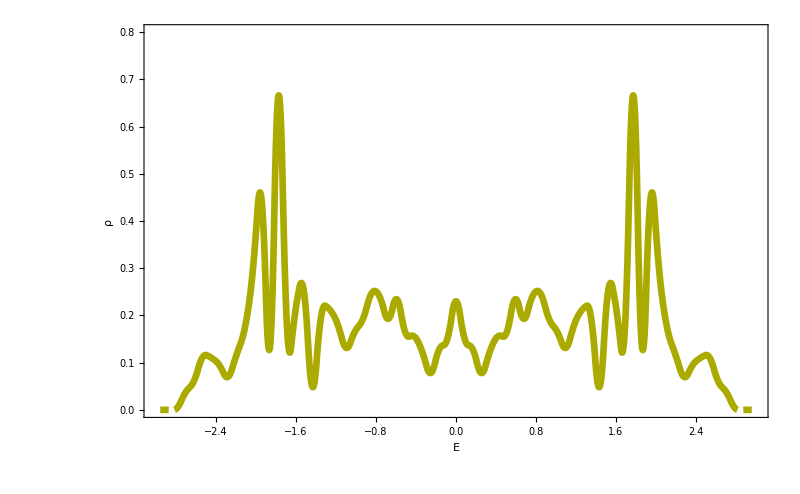

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{{-3,3},{0,0.8}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

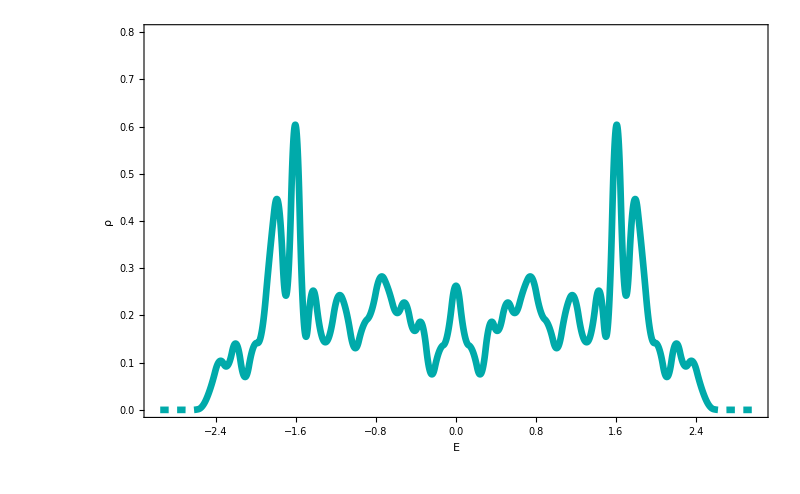

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d4b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d4b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d4hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{{-3,3},{0,0.8}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

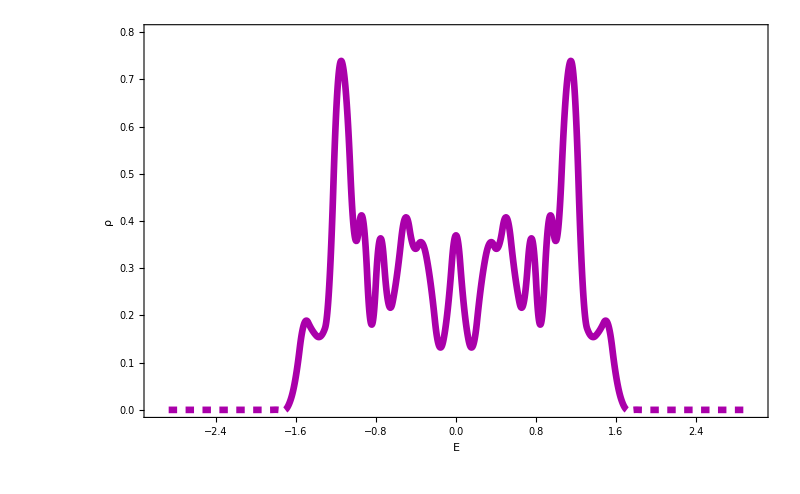

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d8b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d8b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d8hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{{-3,3},{0,0.8}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

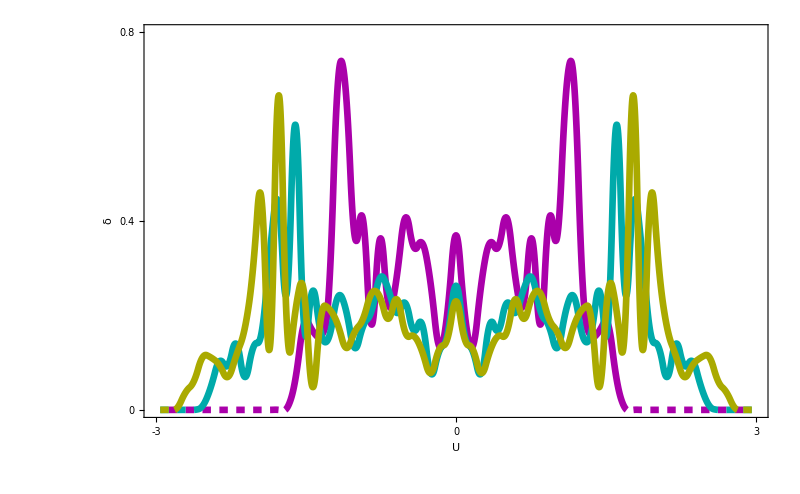

```mathematica
Show[
a0d8hist,a0d4hist,a0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.4,0.8},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
dosnearzero[d_,b_]:=Length[Position[Abs[d],_?(#<=b&)]];
dosnearzeronormalized[d_,b_]:=(Length[Position[Abs[d],_?(#<=b&)]]/Length[d])/(2*b);
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha/DOS_NearZero_Data";
```

```mathematica
buffer=0.09;
```

```mathematica
alphaval="0";
```

```mathematica
a0b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1div2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1div3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1div4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1div6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1div8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div8_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.4";
```

```mathematica
a0d4b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1div2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1div3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1div4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1div6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1div8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div8_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.8";
```

```mathematica
a0d8b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1div2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1div3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1div4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1div6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div6_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1div8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a",alphaval,"_amag1div8_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.4_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.8_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0dosnearzerodata={a0b0d4,a0b0d6,a0b0d8,a0b1,a0b1div2,a0b1div4,a0b1div6,a0b1div8,a0b1div3}-a0b0;
a0d4dosnearzerodata={a0d4b0d4,a0d4b0d6,a0d4b0d8,a0d4b1,a0d4b1div2,a0d4b1div4,a0d4b1div6,a0d4b1div8,a0d4b1div3}-a0d4b0;
a0d8dosnearzerodata={a0d8b0d4,a0d8b0d6,a0d8b0d8,a0d8b1,a0d8b1div2,a0d8b1div4,a0d8b1div6,a0d8b1div8,a0d8b1div3}-a0d8b0;
```

```mathematica
magfluxvals={0.4,0.6,0.8,1,1/2,1/4,1/6,1/8,1/3};
```

```mathematica
psize=0.03;
linethickness=0.006;
```

```mathematica
Needs["PolygonPlotMarkers`"]
```

Get::noopen: Cannot open PolygonPlotMarkers`.

Needs::nocont: Context PolygonPlotMarkers` was not created when Needs was evaluated.

$Failed

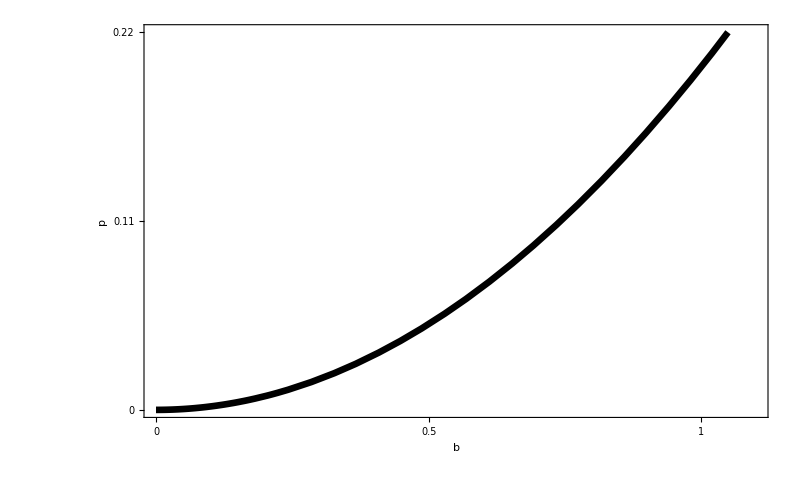

```mathematica
xrange={0,1.1};
yrange={0,0.22};
Show[
Plot[0.2*x^2,{x,0,2},PlotStyle->{Black,Thickness[linethickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{magfluxvals,a0dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Yellow]]],Rectangle[{-1, -1}, {1, 1}]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d4dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Cyan]]],Disk[]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d8dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Magenta]]],Polygon[{{-1, 1},{0, -1},{1 ,1}}]},ImageSize->22],PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"b","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.11,0.22},None},{{0,0.5,1},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha";
```

```mathematica
a0b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d4b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.4_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d8b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.8_amag1.0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

71

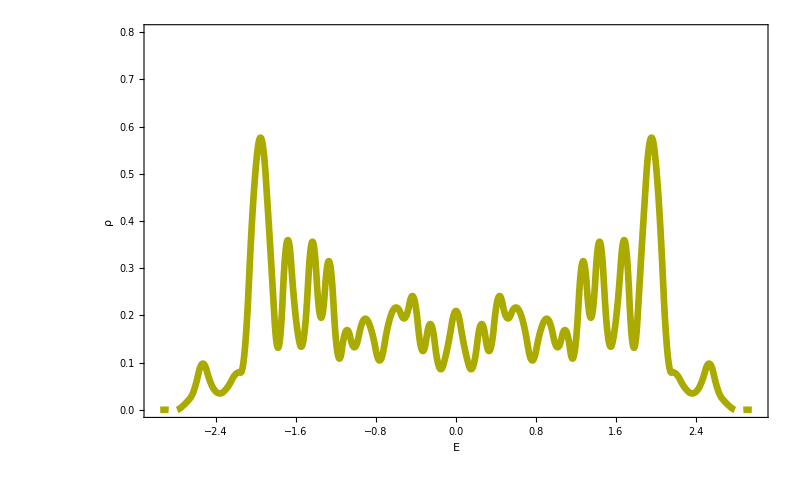

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{{-3,3},{0,0.8}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

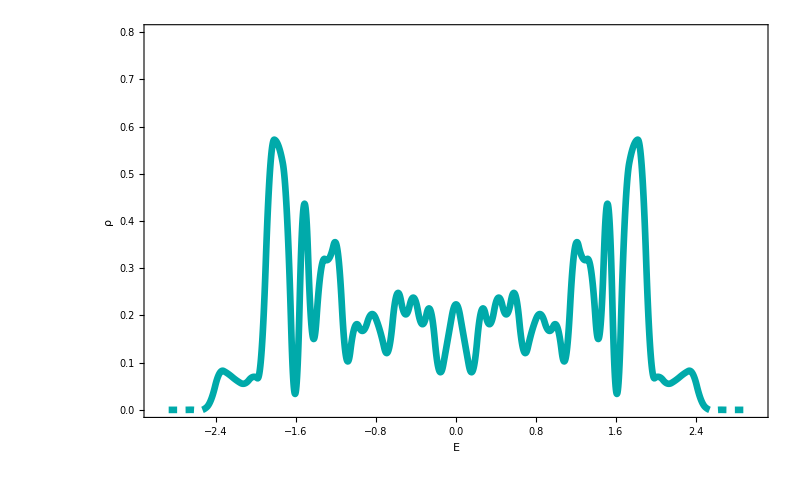

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d4b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d4b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d4hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{{-3,3},{0,0.8}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

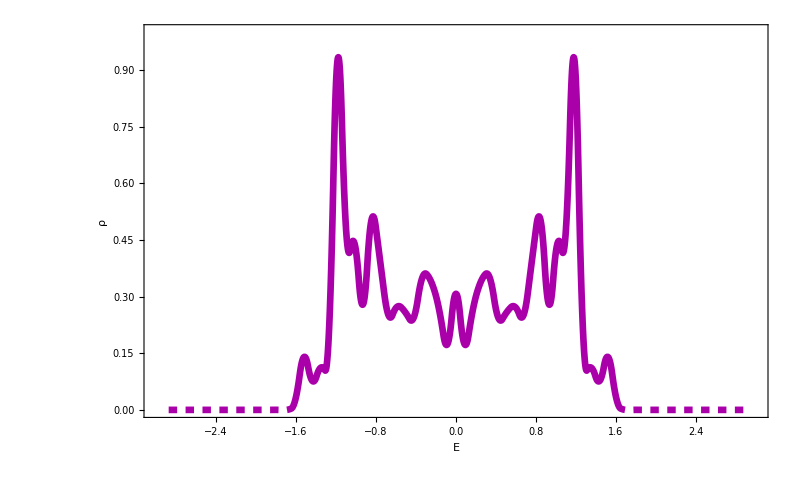

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d8b1data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d8b1data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d8hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{{-3,3},{0,1}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

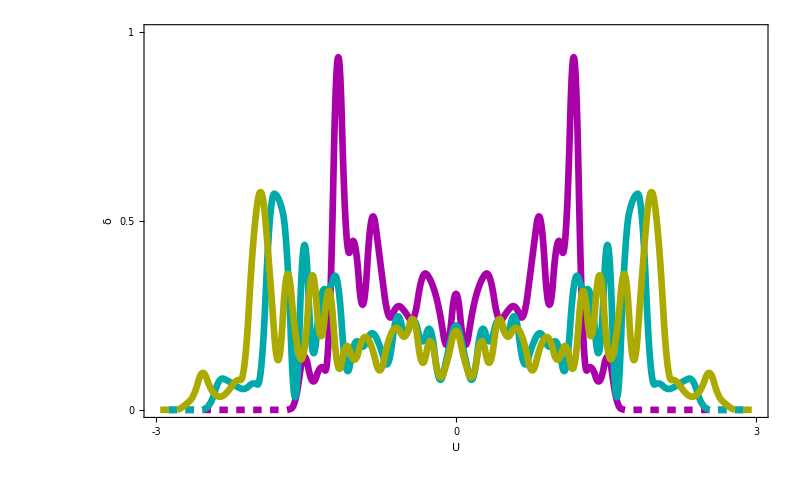

```mathematica
Show[
a0d8hist,a0d4hist,a0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
dosnearzero[d_,b_]:=Length[Position[Abs[d],_?(#<=b&)]];
dosnearzeronormalized[d_,b_]:=(Length[Position[Abs[d],_?(#<=b&)]]/Length[d])/(2*b);
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha/DOS_NearZero_Data";
```

```mathematica
buffer=0.045;
```

```mathematica
alphaval="0";
```

```mathematica
a0b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d7=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d7_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b1d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b2d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag3_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.4";
```

```mathematica
a0d4b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d7=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d7_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b1d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b2d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag3_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.8";
```

```mathematica
a0d8b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d7=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d7_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d8=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag0d8_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b1d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag1d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b2d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag2d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a",alphaval,"_amag3_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.4_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.8_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0dosnearzerodata={a0b0d2,a0b0d35,a0b0d5,a0b0d7,a0b0d8,a0b1,a0b1d2,a0b1d5,a0b2,a0b2d5,a0b3}-a0b0;
a0d4dosnearzerodata={a0d4b0d2,a0d4b0d35,a0d4b0d5,a0d4b0d7,a0d4b0d8,a0d4b1,a0d4b1d2,a0d4b1d5,a0d4b2,a0d4b2d5,a0d4b3}-a0d4b0;
a0d8dosnearzerodata={a0d8b0d2,a0d8b0d35,a0d8b0d5,a0d8b0d7,a0d8b0d8,a0d8b1,a0d8b1d2,a0d8b1d5,a0d8b2,a0d8b2d5,a0d8b3}-a0d8b0;
```

```mathematica
magfluxvals={0.2,0.35,0.5,0.7,0.8,1,1.2,1.5,2,2.5,3};
```

```mathematica
psize=0.03;
linethickness=0.006;
```

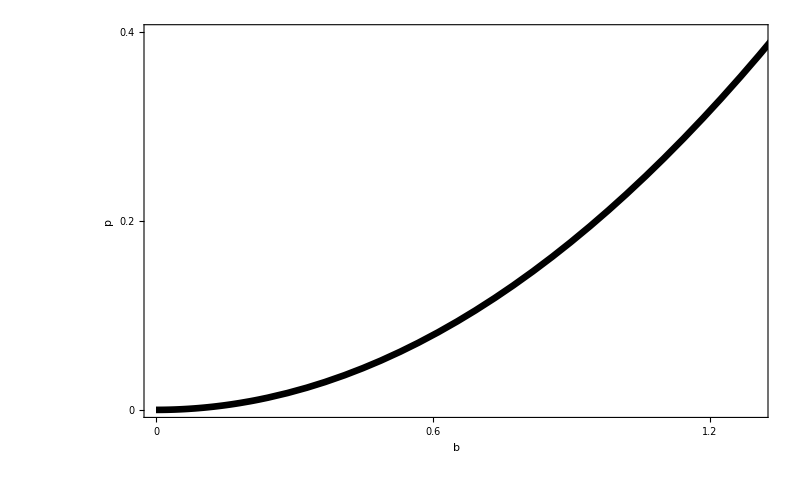

```mathematica
xrange={0,1.3};
yrange={0,0.4};
Show[
Plot[0.22*x^2,{x,0,2},PlotStyle->{Black,Thickness[linethickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{magfluxvals,a0dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Yellow]]],Rectangle[{-1,-1},{1,1}]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d4dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Cyan]]],Disk[]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d8dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Magenta]]],Polygon[{{-1,1},{0,-1},{1,1}}]},ImageSize->22],PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"b","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{0,0.6,1.2},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha";
```

```mathematica
a0b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d4b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag1.0_eigvals.txt"],"Data"])[[1]]]];
a0d8b1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_amag1.0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b0d5data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycomb_nl20_openBC_a0amag0d5_eigvals.txt"],"Data"])[[1]]]];
a0d4b0d5data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycomb_nl20_openBC_a0.4amag0d5_eigvals.txt"],"Data"])[[1]]]];
a0d8b0d5data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycomb_nl20_openBC_a0.8amag0d5_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

71

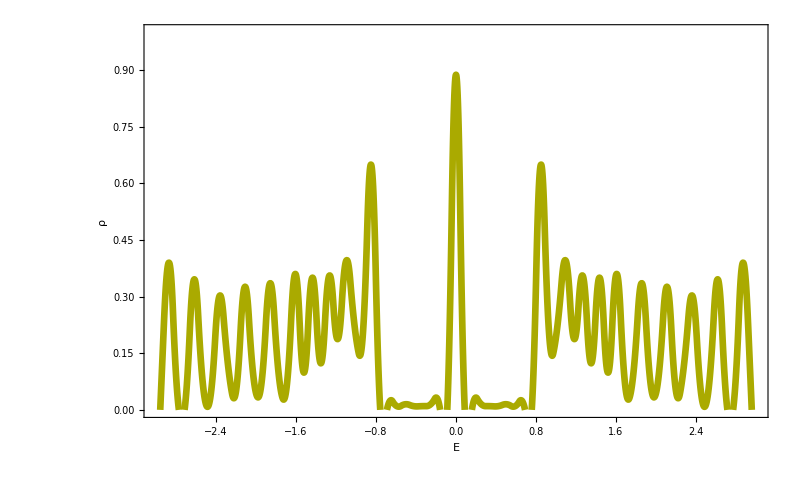

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b0d5data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b0d5data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{{-3,3},{0,1}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

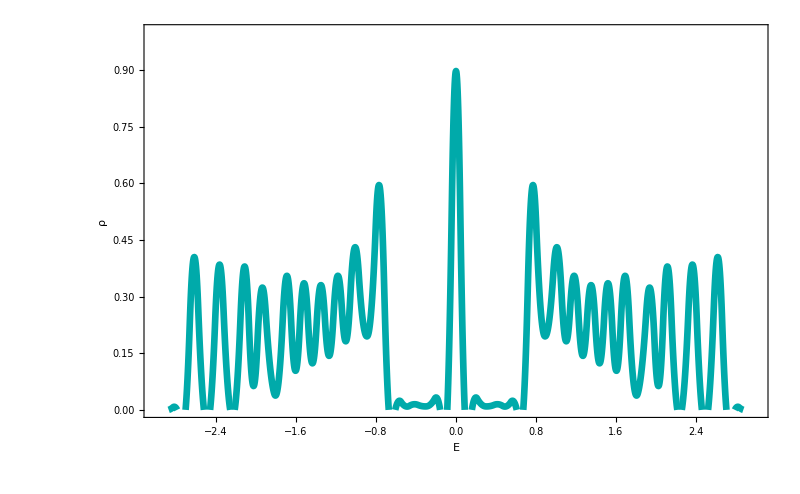

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d4b0d5data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d4b0d5data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d4hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{{-3,3},{0,1}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

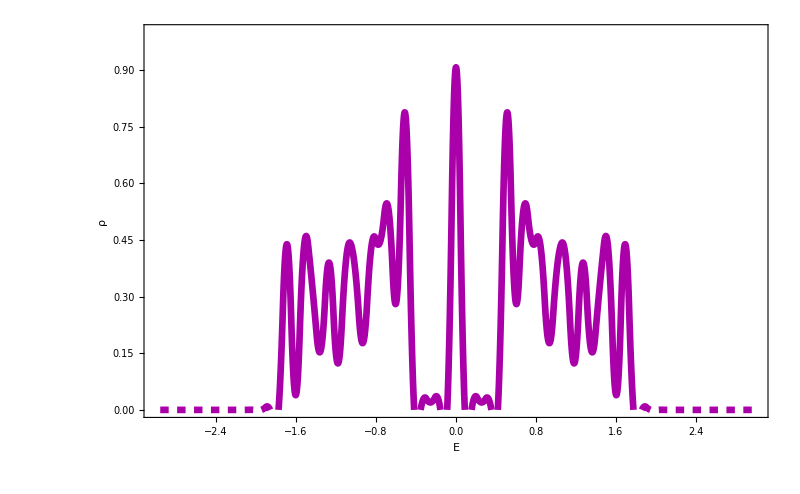

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0d8b0d5data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d8b0d5data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d8hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{{-3,3},{0,1}}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

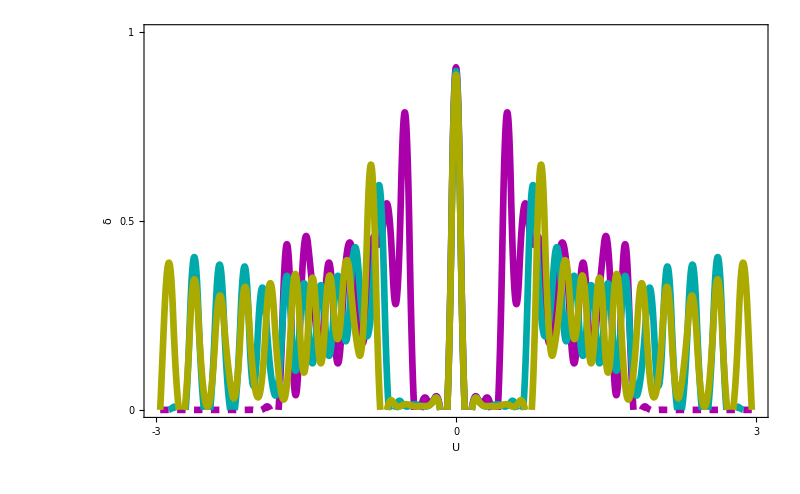

```mathematica
Show[
a0d8hist,a0d4hist,a0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
dosnearzero[d_,b_]:=Length[Position[Abs[d],_?(#<=b&)]];
dosnearzeronormalized[d_,b_]:=(Length[Position[Abs[d],_?(#<=b&)]]/Length[d])/(2*b);
```

```mathematica
datadir="../Processed_Data/3_DOS_FixedMag_VaryAlpha/DOS_NearZero_Data";
```

```mathematica
buffer=0.05;
```

```mathematica
alphaval="0";
```

```mathematica
a0b0d1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d15=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d15_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d25=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d25_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d45=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d45_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d55=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d55_eigvals.txt"],"Data"])[[1]]]],buffer];
a0b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.4";
```

```mathematica
a0d4b0d1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d15=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d15_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d25=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d25_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d45=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d45_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d55=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d55_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
alphaval="0.8";
```

```mathematica
a0d8b0d1=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d1_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d15=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d15_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d2=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d2_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d25=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d25_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d3=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d3_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d35=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d35_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d4=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d4_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d45=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d45_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d5=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d5_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d55=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d55_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0d6=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a",alphaval,"_amag0d6_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d4b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.4_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
a0d8b0=dosnearzeronormalized[Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_amag0_eigvals.txt"],"Data"])[[1]]]],buffer];
```

```mathematica
a0dosnearzerodata={a0b0d1,a0b0d15,a0b0d2,a0b0d25,a0b0d3,a0b0d35,a0b0d4,a0b0d45,a0b0d5,a0b0d55,a0b0d6}-a0b0;
a0d4dosnearzerodata={a0d4b0d1,a0d4b0d15,a0d4b0d2,a0d4b0d25,a0d4b0d3,a0d4b0d35,a0d4b0d4,a0d4b0d45,a0d4b0d5,a0d4b0d55,a0d4b0d6}-a0d4b0;
a0d8dosnearzerodata={a0d8b0d1,a0d8b0d15,a0d8b0d2,a0d8b0d25,a0d8b0d3,a0d8b0d35,a0d8b0d4,a0d8b0d45,a0d8b0d5,a0d8b0d55,a0d8b0d6}-a0d8b0;
```

```mathematica
magfluxvals={0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6};
```

```mathematica
psize=0.03;
linethickness=0.006;
```

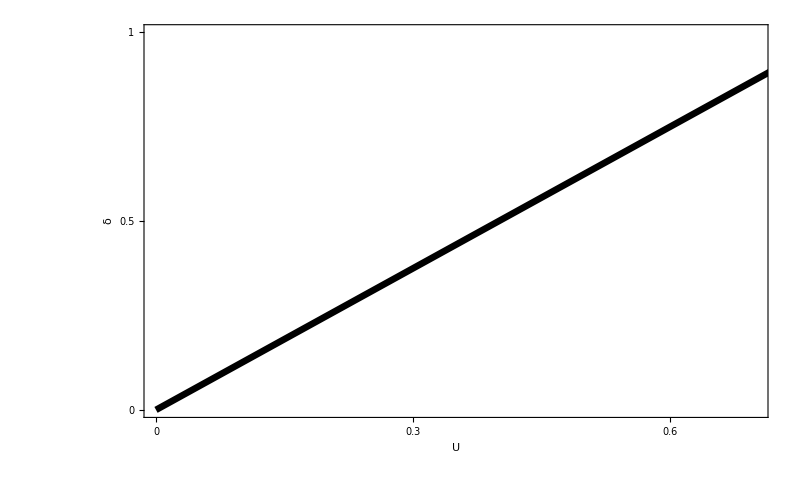

```mathematica
xrange={0,0.7};
yrange={0,1};
Show[
Plot[1.25*x,{x,0,700},PlotStyle->{Black,Thickness[linethickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{magfluxvals,a0dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Yellow]]],Rectangle[{-1,-1},{1,1}]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d4dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Cyan]]],Disk[]},ImageSize->22],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{magfluxvals,a0d8dosnearzerodata},PlotMarkers->Graphics[{FaceForm[Opacity[0]],EdgeForm[Directive[Thick,Darker[Magenta]]],Polygon[{{-1,1},{0,-1},{1,1}}]},ImageSize->22],PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{0,0.3,0.6},None}},FrameTicksStyle->FontSize->50
]
```